```mathematica
Δ110=a1 p11 q11 p11 q11 p10+a0 p01 q01 p11 q11 p10+a0 p01 q00 p01 q01 p10+a1 p11 q10 p01 q01 p10-K (a1 p11 q11 p11 q11 p10+a1 p11 q11 p11 q10 p00+a0 p01 q01 p11 q11 p10+a0 p01 q01 p11 q10 p00+a0 p01 q00 p01 q01 p10+a0 p01 q00 p01 q00 p00+a1 p11 q10 p01 q01 p10+a1 p11 q10 p01 q00 p00)
```

a0 p01^2 p10 q00 q01+a1 p01 p10 p11 q01 q10+a0 p01 p10 p11 q01 q11+a1 p10 p11^2 q11^2-K (a0 p00 p01^2 q00^2+a0 p01^2 p10 q00 q01+a1 p00 p01 p11 q00 q10+a0 p00 p01 p11 q01 q10+a1 p01 p10 p11 q01 q10+a0 p01 p10 p11 q01 q11+a1 p00 p11^2 q10 q11+a1 p10 p11^2 q11^2)

```mathematica
Δ001=a1 p10 q11 p10 q11 p11+a0 p00 q01 p10 q11 p11+a0 p00 q00 p00 q01 p11+a1 p10 q10 p00 q01 p11-K (a1 p10 q11 p10 q11 p11+a1 p10 q11 p10 q10 p01+a0 p00 q01 p10 q11 p11+a0 p00 q01 p10 q10 p01+a0 p00 q00 p00 q01 p11+a0 p00 q00 p00 q00 p01+a1 p10 q10 p00 q01 p11+a1 p10 q10 p00 q00 p01)
```

a0 p00^2 p11 q00 q01+a1 p00 p10 p11 q01 q10+a0 p00 p10 p11 q01 q11+a1 p10^2 p11 q11^2-K (a0 p00^2 p01 q00^2+a0 p00^2 p11 q00 q01+a1 p00 p01 p10 q00 q10+a0 p00 p01 p10 q01 q10+a1 p00 p10 p11 q01 q10+a0 p00 p10 p11 q01 q11+a1 p01 p10^2 q10 q11+a1 p10^2 p11 q11^2)

```mathematica
Reduce[{Δ110>0&&Δ001<0Δ001&&a0==q10/(q10+q01)&&a1==q01/(q10+q01)&&q11==1-q10&&q00==1-q01&&p00==1-p01&&p10==1-p11&&K>0&&K<1&&q01==0.001&&q10==0.01&&p01==0.2&&p11==0.8}]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

0.0286917<K<0.278694&&q10==0.01&&q01==0.001&&a1==0.0909091&&q11==0.99&&q00==0.999&&p11==0.8&&p10==0.2&&p01==0.2&&p00==0.8&&a0==0.909091

```mathematica
Reduce[{Δ110<0&&Δ001>0Δ001&&a0==q10/(q10+q01)&&a1==q01/(q10+q01)&&q11==1-q10&&q00==1-q01&&p00==1-p01&&p10==1-p11&&K>0&&K<1&&q01==0.001&&q10==0.05&&p01==0.0001&&p11==0.8}]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

0.791659<K<0.938717&&q10==0.05&&q01==0.001&&a1==0.0196078&&q11==0.95&&q00==0.999&&p11==0.8&&p10==0.2&&p01==0.0001&&p00==0.9999&&a0==0.980392

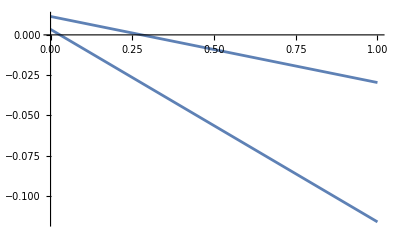

```mathematica
Plot[{Δ110,Δ001}/.a0->q10/(q10+q01)/.a1->q01/(q10+q01)/.q11->1-q10/.q00->1-q01/.p00->1-p01/.p10->1-p11/.q01->0.001/.q10->0.01/.p01->0.2/.p11->0.8,{K,0,1}]
```

```mathematica
Coefficient[{Δ110,Δ001}/.a0->q10/(q10+q01)/.a1->q01/(q10+q01)/.q11->1-q10/.q00->1-q01/.p00->1-p01/.p10->1-p11/.q01->0.001/.q10->0.01/.p01->0.2/.p11->0.8,K,0]
```

{0.0114409,0.00343151}

```mathematica
Coefficient[{Δ110,Δ001}/.a0->q10/(q10+q01)/.a1->q01/(q10+q01)/.q11->1-q10/.q00->1-q01/.p00->1-p01/.p10->1-p11/.q01->0.001/.q10->0.01/.p01->0.2/.p11->0.8,K,1]
```

{-0.0410519,-0.119599}

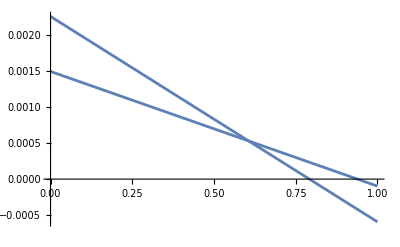

```mathematica
Plot[{Δ110,Δ001}/.a0->q10/(q10+q01)/.a1->q01/(q10+q01)/.q11->1-q10/.q00->1-q01/.p00->1-p01/.p10->1-p11/.q01->0.001/.q10->0.05/.p01->0.0001/.p11->0.8,{K,0,1}]
```

```mathematica
Coefficient[{Δ110,Δ001}/.a0->q10/(q10+q01)/.a1->q01/(q10+q01)/.q11->1-q10/.q00->1-q01/.p00->1-p01/.p10->1-p11/.q01->0.001/.q10->0.05/.p01->0.0001/.p11->0.8,K,0]
```

{0.00226511,0.00149881}

```mathematica
Coefficient[{Δ110,Δ001}/.a0->q10/(q10+q01)/.a1->q01/(q10+q01)/.q11->1-q10/.q00->1-q01/.p00->1-p01/.p10->1-p11/.q01->0.001/.q10->0.05/.p01->0.0001/.p11->0.8,K,1]
```

{-0.00286122,-0.00159666}